```mathematica
$Assumptions={{W>0,G0,G1,G1m,Gm0,T1}∈Reals,W>0,G0>0,G1>0,G1m>0,Gm0>0,T1>0,T2>0};
```

```mathematica
(* G's are the decay rates between various states, W the laser pumping rate *)
```

```mathematica
(* Definition of the Lindbladian superoperator See e.g. doi:10.1063/1.1518555 *)
```

```mathematica
Lindblad[L_]:=Block[{nL=Length[L],n=Dimensions[L]⟦2⟧},-∑_k^nL (Kron[Conjugate[L⟦k⟧],L⟦k⟧]-1/2 Kron[Id[n],ConjugateTranspose[L⟦k⟧].L⟦k⟧]-1/2 Kron[ConjugateTranspose[Conjugate[L⟦k⟧]].Conjugate[L⟦k⟧],Id[n]])]
```

```mathematica
(* just a useful matrix with all zeros and 1 at jk *)
```

```mathematica
Ljk[j_,k_]:=Partition[ReplacePart[Table[0,{25}],(j-1)*5+k->1],5]
```

```mathematica
(* Full superoperator *)
```

```mathematica
H=PadRight[Kron[ep,(Δg-γ B)z]+Kron[em,(Δe-γ B)z],{5,5}];
```

```mathematica
H//mf
```

(-B γ+Δg | 0 | 0 | 0 | 0
0 | B γ-Δg | 0 | 0 | 0
0 | 0 | -B γ+Δg | 0 | 0
0 | 0 | 0 | B γ-Δg | 0
0 | 0 | 0 | 0 | 0)

```mathematica
MP=-I(Kron[H,Id[5]]-Kron[Id[5],H])-Lindblad[{Sqrt[G0] Ljk[1,3],Sqrt[G1] Ljk[2,4],Sqrt[W] Ljk[3,1],0Sqrt[W] Ljk[1,3],0Sqrt[W] Ljk[2,4],Sqrt[W] Ljk[4,2],Sqrt[G1m] Ljk[5,4],Sqrt[Gm0] Ljk[1,5],Sqrt[1/(2T1)]Ljk[1,2],Sqrt[1/(2T1)]Ljk[2,1],Sqrt[1/(2 T2)](Ljk[1,1]-Ljk[2,2])}];
```

```mathematica
(* Propagator *)
```

```mathematica
Sp[t_]:=MatrixExp[MP t]
```

```mathematica
(* Density matrix in Liouville space (it's a vector) *)
```

```mathematica
rho[t_,r0_]:=Partition[Sp[t].Flatten[r0,1],5]
```

```mathematica
(* Evolution of the various populations from the mixed state (or generally from r0) *)
```

```mathematica
Block[{Δg=2.87 10^3,Δe=1.42 10^3,γ=2.8,B=50,r0=(Ljk[1,1]+Ljk[2,2])/2,Wmw=0,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1,W=30},Plot[{rho[t,r0][[1,1]],rho[t,r0][[2,2]],rho[t,r0][[3,3]],rho[t,r0][[4,4]],rho[t,r0][[5,5]]},{t,0,1},PlotRange->All,PlotStyle -> {{Red,Thick},{Purple,Thick,Dashing[.01]},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```

1 ground state of 0
2 ground state of 1
3 excited state of 0
4 excited state of 1
5 Metastable state

Δg:Zero field splitting
Δe:
γ:Gyromagnetic ratio
r0:Initial state matrix
Wmw:
G0:Spontaneous decay rate in 0 state
G1:Spontaneous decay rate in 1 state
G1m:decay from 1 excited to metastable
Gm0:decay from metastable to 0
W:Pumping rate

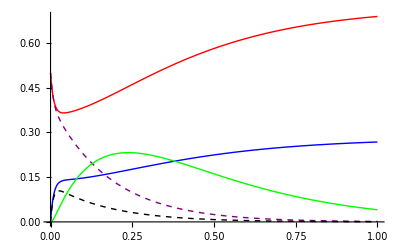

Red: 0 state
Purpule: 1 state
Blue:

```mathematica
(* The Zeeman + zero field splitting do not matter: *)
```

```mathematica
MP=-Lindblad[{Sqrt[G0] Ljk[1,3],Sqrt[G1] Ljk[2,4],Sqrt[W] Ljk[3,1],0Sqrt[W] Ljk[1,3],0Sqrt[W] Ljk[2,4],Sqrt[W] Ljk[4,2],Sqrt[G1m] Ljk[5,4],Sqrt[Gm0] Ljk[1,5],Sqrt[1/(2T1)]Ljk[1,2],Sqrt[1/(2T1)]Ljk[2,1],Sqrt[1/(2 T2)](Ljk[1,1]-Ljk[2,2])}];
```

```mathematica
Block[{Δg=2.87 10^3,Δe=1.42 10^3,γ=2.8,B=50,r0=(Ljk[1,1]+Ljk[2,2])/2,Wmw=0,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1,W=30},Plot[{rho[t,r0][[1,1]],rho[t,r0][[2,2]],rho[t,r0][[3,3]],rho[t,r0][[4,4]],rho[t,r0][[5,5]]},{t,0,1},PlotRange->All,PlotStyle -> {{Red,Thick},{Purple,Thick,Dashing[.01]},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```

-Graphics-

## Time-dependent Fluorescence emission

```mathematica
(* Fluorescence Emission starting from 1 or 0: the +1 state emits radiatively only 2/3 of the time (it's otherwise going in the metastable singlet) *)
```

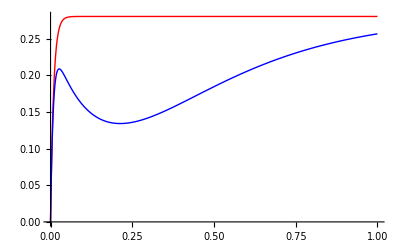

```mathematica
Block[{r0=Ljk[1,1],r1=Ljk[2,2],Wmw=0,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1,W=30},Plot[{rho[t,r0][[3,3]]+3/3rho[t,r0][[4,4]],rho[t,r1][[3,3]]+3/3rho[t,r1][[4,4]]},{t,0,1},PlotRange->All,PlotStyle -> {{Red,Thick},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```

```mathematica
(* Now add a uwave field on resonance in the ground state (So I'm neglecting all other terms of the Hamiltonian, should be reintroduced for precision) *)
```

```mathematica
H= Wmw (Ljk[1,2]+Ljk[2,1]);
```

```mathematica
MP=-I(Kron[H,Id[5]]-Kron[Id[5],H])-Lindblad[{Sqrt[G0] Ljk[1,3],Sqrt[G1] Ljk[2,4],Sqrt[W] Ljk[3,1],0Sqrt[W] Ljk[1,3],0Sqrt[W] Ljk[2,4],Sqrt[W] Ljk[4,2],Sqrt[G1m] Ljk[5,4],Sqrt[Gm0] Ljk[1,5],Sqrt[1/(2T1)]Ljk[1,2],Sqrt[1/(2T1)]Ljk[2,1],Sqrt[1/(2 T2)](Ljk[1,1]-Ljk[2,2])}];
```

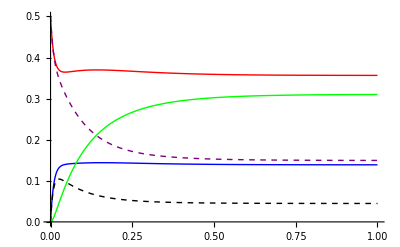

```mathematica
Block[{Wmw=10,r0=(Ljk[1,1]+Ljk[2,2])/2,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1,W=30},Plot[{rho[t,r0][[1,1]],rho[t,r0][[2,2]],rho[t,r0][[3,3]],rho[t,r0][[4,4]],rho[t,r0][[5,5]]},{t,0,1},PlotRange->All,PlotStyle -> {{Red,Thick},{Purple,Thick,Dashing[.01]},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```

```mathematica
(* Fluorescence Emission starting from 1 or 0: the +1 state emits radiatively only 2/3 of the time *)
```

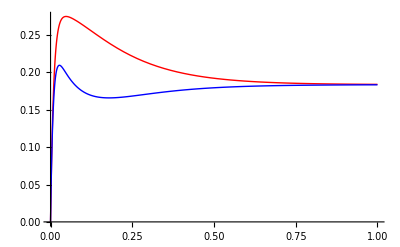

```mathematica
Block[{r0=Ljk[1,1],r1=Ljk[2,2],Wmw=10,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1,W=30},Plot[{rho[t,r0][[3,3]]+3/3rho[t,r0][[4,4]],rho[t,r1][[3,3]]+3/3rho[t,r1][[4,4]]},{t,0,1},PlotRange->All,PlotStyle -> {{Red,Thick},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```

## This is what is needed to calculate the CW spectrum

```mathematica
(* If the uwave is off resonance by Δω, we have *)
```

```mathematica
H= Wmw (Ljk[1,2]+Ljk[2,1])+PadRight[Kron[ep,Δω z]+Kron[em,(Δe-γ B)z],{5,5}];
```

```mathematica
MP=-I(Kron[H,Id[5]]-Kron[Id[5],H])-Lindblad[{Sqrt[G0] Ljk[1,3],Sqrt[G1] Ljk[2,4],Sqrt[W] Ljk[3,1],0Sqrt[W] Ljk[1,3],0Sqrt[W] Ljk[2,4],Sqrt[W] Ljk[4,2],Sqrt[G1m] Ljk[5,4],Sqrt[Gm0] Ljk[1,5],Sqrt[1/(2T1)]Ljk[1,2],Sqrt[1/(2T1)]Ljk[2,1],Sqrt[1/(2 T2)](Ljk[1,1]-Ljk[2,2])}];
```

```mathematica
Diagonal[MP]/.T1->∞/.T2->∞/.Δe->0/.B->0//fs
```

{-W,-W-2 ⅈ Δω,1/2 (-G0-W-2 ⅈ Δω),1/2 (-G1-G1m-W-2 ⅈ Δω),1/2 (-Gm0-W-2 ⅈ Δω),-W+2 ⅈ Δω,-W,1/2 (-G0-W+2 ⅈ Δω),1/2 (-G1-G1m-W+2 ⅈ Δω),1/2 (-Gm0-W+2 ⅈ Δω),1/2 (-G0-W+2 ⅈ Δω),1/2 (-G0-W-2 ⅈ Δω),-G0,1/2 (-G0-G1-G1m),1/2 (-G0-Gm0),1/2 (-G1-G1m-W+2 ⅈ Δω),1/2 (-G1-G1m-W-2 ⅈ Δω),1/2 (-G0-G1-G1m),-G1-G1m,1/2 (-G1-G1m-Gm0),1/2 (-Gm0-W+2 ⅈ Δω),1/2 (-Gm0-W-2 ⅈ Δω),1/2 (-G0-Gm0),1/2 (-G1-G1m-Gm0),-Gm0}

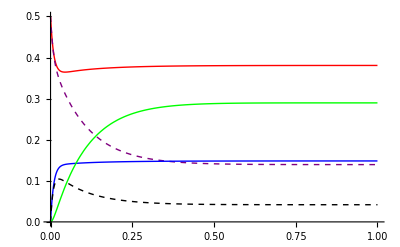

```mathematica
Block[{Wmw=10,Δω=10,Δe=1.42 10^3,γ=2.8,B=50,r0=(Ljk[1,1]+Ljk[2,2])/2,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1,W=30},Plot[{rho[t,r0][[1,1]],rho[t,r0][[2,2]],rho[t,r0][[3,3]],rho[t,r0][[4,4]],rho[t,r0][[5,5]]},{t,0,1},PlotRange->All,PlotStyle -> {{Red,Thick},{Purple,Thick,Dashing[.01]},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```

```mathematica
(* The fluorescence Emission starting from a mixed state depends on how far off resonance is the uwave field (less emission on resonance) *)
```

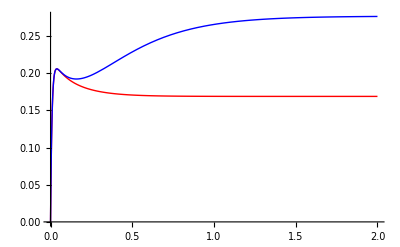

```mathematica
Block[{Wmw=10,Δe=1.42 10^3,γ=2.8,B=50,r0=(Ljk[1,1]+Ljk[2,2])/2,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1,W=30},Plot[{Block[{Δω=0},rho[t,r0][[3,3]]+2/3rho[t,r0][[4,4]]],Block[{Δω=200},rho[t,r0][[3,3]]+2/3rho[t,r0][[4,4]]]},{t,0,2},PlotRange->All,PlotStyle -> {{Red,Thick},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```

```mathematica
(* Laser Power Broadening *)
```

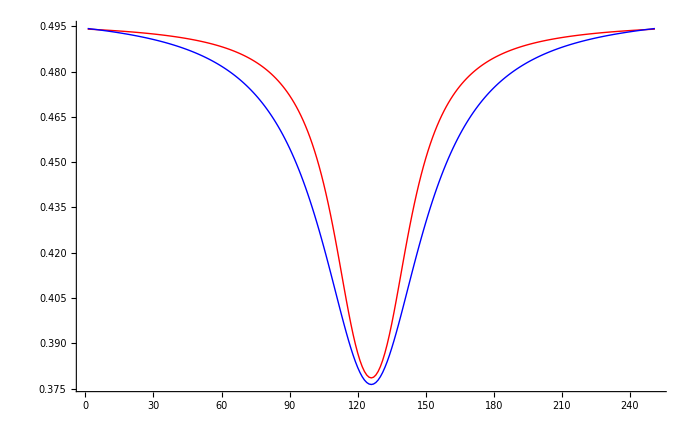

```mathematica
Block[{Wmw=10,Δe=1.42 10^3,γ=2.8,B=50,r0=(Ljk[1,1]+Ljk[2,2])/2,G0=77,G1=77,G1m=0.3 77,Gm0=1/0.3,T1=10^4,T2=.1},ListPlot[{Block[{W=1},-.429+85.8Re[Table[Block[{Δω=k-250},rho[2.5,r0][[3,3]]+2/3rho[2.5,r0][[4,4]]],{k,0,500,2}]]],Block[{W=77},Re[Table[Block[{Δω=k-250},rho[2.5,r0][[3,3]]+2/3rho[2.5,r0][[4,4]]],{k,0,500,2}]]]},PlotRange->All,Joined->True,PlotStyle -> {{Red,Thick},{Blue,Thick},{Black,Thick,Dashing[.01]},{Green,Thick}}]]
```